# Andrea Halenkamp

### Question 8

```mathematica
f[t_,x_]:=(t+2)/x;
```

```mathematica
xe[t_]:=Sqrt[(t+2)^2];
```

Direction Field and Curve

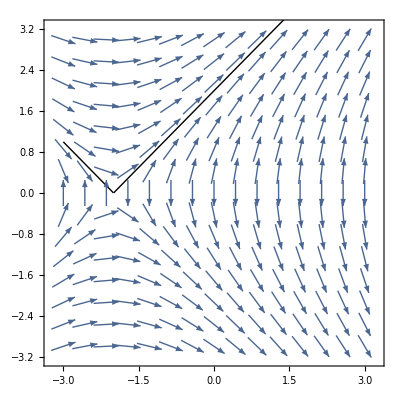

```mathematica
Show[VectorPlot[{1,f[t,x]},{t,-3,3},{x,-3,3},Axes->True,Frame->True,VectorScale->{Small,Automatic,None}],Plot[xe[t],{t,-3,3},PlotStyle->{Thick,Black}]]
```

Evaluate exact solution from 0 to 1.5 with a step size of 0.125

```mathematica
exactSolutions=Table[xe[t],{t,0,1.5,0.125}];
```

Euler’s method with Δt = 0.125 and steps = 12

```mathematica
steps=12;
Δt=.125; 
t=0;  
x=2;
solutionLessSteps={{t,x}};
Do[
x=x+Δt*f[t,x];
t=t+Δt;
AppendTo[solutionLessSteps,{t,x}];
,{steps}];
solutionLessSteps
```

{{0,2},{0.125,2.125},{0.25,2.25},{0.375,2.375},{0.5,2.5},{0.625,2.625},{0.75,2.75},{0.875,2.875},{1.,3.},{1.125,3.125},{1.25,3.25},{1.375,3.375},{1.5,3.5}}

Euler’s method with Δt = 0.0625 and steps = 24

```mathematica
Clear[steps,Δt,t,x];
steps=24;
Δt= 0.0625; 
t=0;  
x=2;
solutionMoreSteps={{t,x}};
Do[
x=x+Δt*f[t,x];
t=t+Δt;
AppendTo[solutionMoreSteps,{t,x}];
,{steps}];
solutionMoreSteps
```

{{0,2},{0.0625,2.0625},{0.125,2.125},{0.1875,2.1875},{0.25,2.25},{0.3125,2.3125},{0.375,2.375},{0.4375,2.4375},{0.5,2.5},{0.5625,2.5625},{0.625,2.625},{0.6875,2.6875},{0.75,2.75},{0.8125,2.8125},{0.875,2.875},{0.9375,2.9375},{1.,3.},{1.0625,3.0625},{1.125,3.125},{1.1875,3.1875},{1.25,3.25},{1.3125,3.3125},{1.375,3.375},{1.4375,3.4375},{1.5,3.5}}

#### Compare

```mathematica
TableForm[Table[{solutionLessSteps[[i,1]],exactSolutions[[i]],solutionLessSteps[[i,2]],Abs[exactSolutions[[i]]-solutionLessSteps[[i,2]]],solutionMoreSteps[[2*i-1,2]],Abs[exactSolutions[[i]]-solutionMoreSteps[[2*i-1,2]]]},{i,11}],TableHeadings->{None,{"t","Exact","Euler with Δt = .125","Error","Euler with Δt = .0625","Error"}}]
```

t | Exact | Euler with Δt = .125 | Error | Euler with Δt = .0625 | Error
0 | 2. | 2 | 0. | 2 | 0.
0.125 | 2.125 | 2.125 | 0. | 2.125 | 0.
0.25 | 2.25 | 2.25 | 0. | 2.25 | 0.
0.375 | 2.375 | 2.375 | 0. | 2.375 | 0.
0.5 | 2.5 | 2.5 | 0. | 2.5 | 0.
0.625 | 2.625 | 2.625 | 0. | 2.625 | 0.
0.75 | 2.75 | 2.75 | 0. | 2.75 | 0.
0.875 | 2.875 | 2.875 | 0. | 2.875 | 0.
1. | 3. | 3. | 0. | 3. | 0.
1.125 | 3.125 | 3.125 | 0. | 3.125 | 0.
1.25 | 3.25 | 3.25 | 0. | 3.25 | 0.

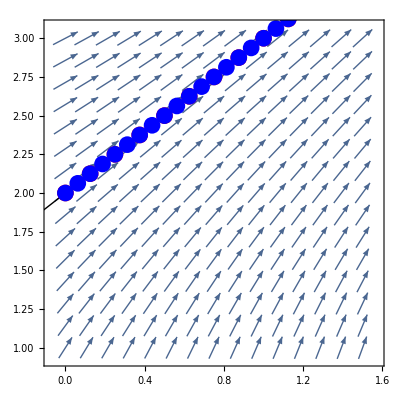

```mathematica
Show[VectorPlot[{1,f[t,x]},{t,0,1.5},{x,1,3},Axes->True,Frame->True,VectorScale->{Small,Automatic,None}],Plot[xe[t],{t,-3,3},PlotStyle->{Thick,Black}],Graphics[{PointSize[.03],Red,Point[solutionLessSteps]}],Graphics[{PointSize[.03],Blue,Point[solutionMoreSteps]}]]
```

There is no error due to the fact the line does not really change direction at all from x=0 onward.

```mathematica
Clear[f,x,exactSolutions,steps,solutionLessSteps,Δt,t,x,solutionMoreSteps]
```

### Question 9

```mathematica
f[t_,x_]:=ⅇ^(-0.2t)Sin[t]-x/5;
```

```mathematica
xe[t_]:=(-Cos[t]+3)/ⅇ^(t/5);
```

Direction Field and Curve

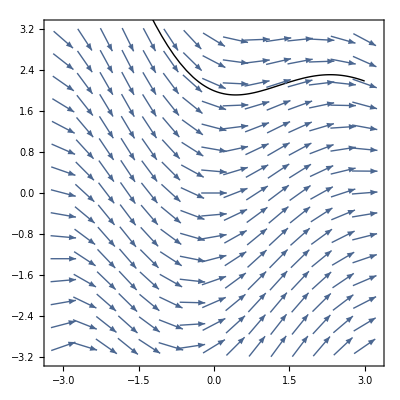

```mathematica
Show[VectorPlot[{1,f[t,x]},{t,-3,3},{x,-3,3},Axes->True,Frame->True,VectorScale->{Small,Automatic,None}],Plot[xe[t],{t,-3,3},PlotStyle->{Thick,Black}]]
```

Evaluate exact solution from 0 to 1.5 with a step size of 0.125

```mathematica
exactSolutions=Table[xe[t],{t,0,1.5,0.125}];
```

Euler’s method with Δt = 0.125 and steps = 12

```mathematica
steps=12;
Δt=.125; 
t=0;  
x=2;
solutionLessSteps={{t,x}};
Do[
x=x+Δt*f[t,x];
t=t+Δt;
AppendTo[solutionLessSteps,{t,x}];
,{steps}];
solutionLessSteps
```

{{0,2},{0.125,1.95},{0.25,1.91645},{0.375,1.89796},{0.5,1.89298},{0.625,1.89988},{0.75,1.91693},{0.875,1.94234},{1.,1.97432},{1.125,2.01108},{1.25,2.05087},{1.375,2.09198},{1.5,2.13281}}

Euler’s method with Δt = 0.0625 and steps = 24

```mathematica
Clear[steps,Δt,t,x];
steps=24;
Δt= 0.0625; 
t=0;  
x=2;
solutionMoreSteps={{t,x}};
Do[
x=x+Δt*f[t,x];
t=t+Δt;
AppendTo[solutionMoreSteps,{t,x}];
,{steps}];
solutionMoreSteps
```

{{0,2},{0.0625,1.975},{0.125,1.95417},{0.1875,1.93734},{0.25,1.92435},{0.3125,1.915},{0.375,1.90911},{0.4375,1.90649},{0.5,1.90692},{0.5625,1.91019},{0.625,1.9161},{0.6875,1.92442},{0.75,1.93493},{0.8125,1.94741},{0.875,1.96164},{0.9375,1.97739},{1.,1.99444},{1.0625,2.01257},{1.125,2.03156},{1.1875,2.05119},{1.25,2.07126},{1.3125,2.09157},{1.375,2.1119},{1.4375,2.13206},{1.5,2.15188}}

#### Compare

```mathematica
TableForm[Table[{solutionLessSteps[[i,1]],exactSolutions[[i]],solutionLessSteps[[i,2]],Abs[exactSolutions[[i]]-solutionLessSteps[[i,2]]],solutionMoreSteps[[2*i-1,2]],Abs[exactSolutions[[i]]-solutionMoreSteps[[2*i-1,2]]]},{i,11}],TableHeadings->{None,{"t","Exact","Euler with Δt = .125","Error","Euler with Δt = .0625","Error"}}]
```

t | Exact | Euler with Δt = .125 | Error | Euler with Δt = .0625 | Error
0 | -1. | 2 | 3. | 2 | 3.
0.125 | -0.9677 | 1.95 | 2.9177 | 1.95417 | 2.92187
0.25 | -0.921658 | 1.91645 | 2.83811 | 1.92435 | 2.846
0.375 | -0.863272 | 1.89796 | 2.76123 | 1.90911 | 2.77238
0.5 | -0.79407 | 1.89298 | 2.68705 | 1.90692 | 2.70099
0.625 | -0.715672 | 1.89988 | 2.61556 | 1.9161 | 2.63177
0.75 | -0.62977 | 1.91693 | 2.5467 | 1.93493 | 2.5647
0.875 | -0.538089 | 1.94234 | 2.48043 | 1.96164 | 2.49973
1. | -0.442362 | 1.97432 | 2.41669 | 1.99444 | 2.4368
1.125 | -0.344301 | 2.01108 | 2.35538 | 2.03156 | 2.37586
1.25 | -0.245573 | 2.05087 | 2.29644 | 2.07126 | 2.31684

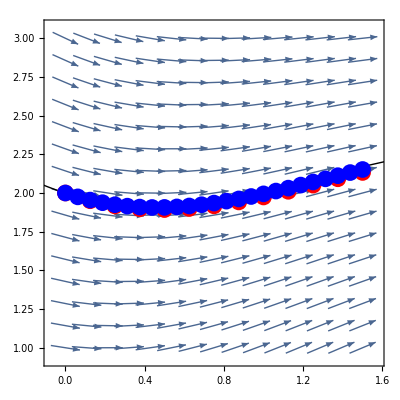

```mathematica
Show[VectorPlot[{1,f[t,x]},{t,0,1.5},{x,1,3},Axes->True,Frame->True,VectorScale->{Small,Automatic,None}],Plot[xe[t],{t,-3,3},PlotStyle->{Thick,Black}],Graphics[{PointSize[.03],Red,Point[solutionLessSteps]}],Graphics[{PointSize[.03],Blue,Point[solutionMoreSteps]}]]
```

There is no error due to the fact the line does not really change direction at all from x=0 onward.

```mathematica
Clear[f,x,exactSolutions,steps,solutionLessSteps,Δt,t,x,solutionMoreSteps]
```